```mathematica
SetDirectory[NotebookDirectory[]];
HotQCDp=Flatten[Import["../fluctuations_T/LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../fluctuations_T/LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../fluctuations_T/LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../fluctuations_T/LQCDdata/hotdpt4u.dat"]];
Tcl=156;
Hotpdown=Transpose[{HotQCDT,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../fluctuations_T/LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../fluctuations_T/LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../fluctuations_T/LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT,WBp-WBdp}];
WBup=Transpose[{WBT,WBp+WBdp}];
WBcs=Table[Import["../fluctuations_T/LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../fluctuations_T/LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT,WBcs-WBcserr}];
V1=Flatten[Import["./eos/eos/BUFFER/VTOTAL.DAT"]];
T1=Table[i,{i,1,Length[V1]}];
p1=(V1[[1]]-V1)/T1^4;
V2=Flatten[Import["./eos_fixedPolya/BUFFER/VTOTAL.DAT"]];
T2=Flatten[Import["./eos_fixedPolya/BUFFER/TMEV.DAT"]];
p2=(V2[[1]]-V2)/T2^4;
V3=Flatten[Import["./eos_fixedPolya_v2/BUFFER/VTOTAL.DAT"]];
T3=Flatten[Import["./eos_fixedPolya_v2/BUFFER/TMEV.DAT"]];
p3=(V3[[1]]-V3)/T3^4;

V4=Flatten[Import["./eos_fixedPolya_v3/BUFFER/VTOTAL.DAT"]];
T4=Flatten[Import["./eos_fixedPolya_v3/BUFFER/TMEV.DAT"]];
p4=(V4[[1]]-V4)/T4^4;

V5=Flatten[Import["./eos_fixedPolya_v4/BUFFER/VTOTAL.DAT"]];
T5=Flatten[Import["./eos_fixedPolya_v4/BUFFER/TMEV.DAT"]];
p5=(V5[[1]]-V5)/T5^4;

V6=Flatten[Import["./eos_fixedPolya_v5/BUFFER/VTOTAL.DAT"]];
T6=Flatten[Import["./eos_fixedPolya_v5/BUFFER/TMEV.DAT"]];
p6=(V6[[1]]-V6)/T6^4;

V7=Flatten[Import["./eos_fixedPolya_v6/BUFFER/VTOTAL.DAT"]];
T7=Flatten[Import["./eos_fixedPolya_v6/BUFFER/TMEV.DAT"]];
p7=(V7[[1]]-V7)/T7^4;

V8=Flatten[Import["./eos_fixedPolya_v7/BUFFER/VTOTAL.DAT"]];
T8=Flatten[Import["./eos_fixedPolya_v7/BUFFER/TMEV.DAT"]];
p8=Transpose[{T8,(V8[[1]]-V8)/T8^4}];

V9=Flatten[Import["./eos_fixedPolya_v8/BUFFER/VTOTAL.DAT"]];
T9=Flatten[Import["./eos_fixedPolya_v8/BUFFER/TMEV.DAT"]];
p9=Transpose[{T9,(V9[[1]]-V9)/T9^4}];

V10=Flatten[Import["./eos_fixedPolya_v9/BUFFER/VTOTAL.DAT"]];
T10=Flatten[Import["./eos_fixedPolya_v9/BUFFER/TMEV.DAT"]];
p10=Transpose[{T10,(V10[[1]]-V10)/T10^4}];

V11=Flatten[Import["./eos_fixedPolya_v10/BUFFER/VTOTAL.DAT"]];
T11=Flatten[Import["./eos_fixedPolya_v10/BUFFER/TMEV.DAT"]];
p11=Transpose[{T11,(V11[[1]]-V11)/T11^4}];
```

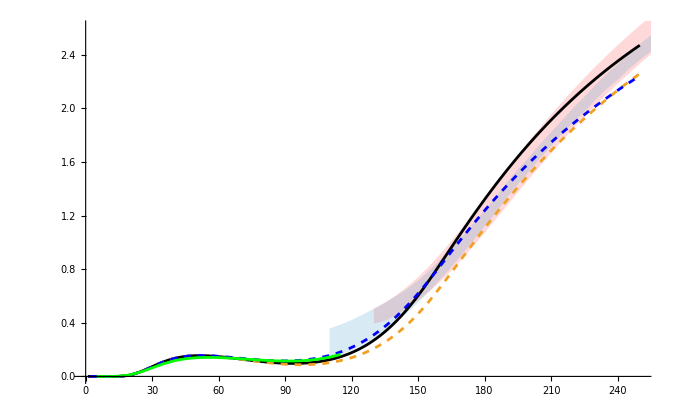

```mathematica
Show[ListLinePlot[{Hotpdown,Hotpup},Filling->{1->{2}},FillingStyle->LightRed,PlotStyle->{None,None}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],ListLinePlot[{(*p1,p2,p3,p4,*)p5,p8,p9(*,p10*),p11},PlotStyle->{Black,Dashed,{Blue,Dashed},Green,Red,Blue,Magenta}],PlotRange->{{0,250},{0,2.6}},AxesOrigin->{0,0.}]
```